## This code is to generate the SIGW, Ω_GW(α,β;k), by a broad broken power-law spectrum with αβ >6

## Setup

```mathematica
α=4;β=4;λ=α/β;
kRange=Power[10,Range[-3,1,1/50]];(*normal scale plot, we have to use exact input instead of machine-precision input to get high precision*)
```

```mathematica
ΔLN=(α β)^(-1/2);
kRangeLN=Power[10,Range[-3.0,1.0,1.0/50]]; (*log scale plot*)
```

```mathematica
Ppl=(α+β)/(α k^β+β k^-α); (*Power spectrum*)
km=((α+β)/β)^(-1/α);kp=((α+β)/α)^(1/β);k0=1;
```

### Q(x,k)Define coefficients in I_y(x,q)

```mathematica
(*(4-γ[q])/x^2*)
```

```mathematica
CyFull=4/x^2-(α β)/x^2(-q^(2 (α+β)) α+β+q^(α+β) (α+α^2+2 α β+(-1+β) β))/((q^(α+β) α+β)^2)/.q->(k x)/(√2);
```

```mathematica
(*Subscript[I, y,p](x,q)*)
QySeries[c_]:=(8 √2)/15+(4 √2)/105 c;
QyA[c_]:=(-c/Ppi+((8 √2)/15)^-2)^(-1/2)/.Ppi->4;
```

```mathematica
Q1inf=QySeries[2/3(4+β)];
QPeak=(8 √Ppi (225 √2 Ppi +64 k^3 x (α β-4)))/((225 Ppi +64 k^2(α β-4))^(3/2))/.Ppi->4;
```

```mathematica
(*Subscript[I, y](x,q),"Normal Approximation"*)
QyN[c_]:=Piecewise[{{(8 √2)/15,c==0}},-(√2 (3+c) ⅇ^(c/2))/c^2+((3+2 c+c^2) √π Erfi[(√c)/(√2)])/c^(5/2)];
Q1m=QyN[CyFull/.{x->√(3/2),q->(√3)/2 k}]//Simplify;
```

```mathematica
(*Subscript[I, y](x,q<κ_-)=am + bm x^-2;  
Subscript[I, y](x,q>κ_+)=(8 √2)/15+ap x^-2-bp x^-4;*)
```

```mathematica
am=(3 k^2 Q1m-4 km^2 QPeak)/(3 k^2-4 km^2)/.x->(√2 km)/k;
bm=(6 km^2 (Q1m-QPeak))/(-3 k^2+4 km^2)/.x->(√2 km)/k;
ap=(4 √2)/105 (4+β);
bp=x^4(QPeak-(8 √2)/15-(4 √2)/105  (4+β)x^-2)/.x->(√2 kp)/k//Simplify;
```

### P_R

```mathematica
Pkp=Ppl/.k->kp//PowerExpand//Simplify;
Pkm=Ppl/.k->km//PowerExpand//Simplify;
```

## Parallel set up

```mathematica
(*My computer has 16 kenerls. Remember to change this value based on your computer*)
```

```mathematica
LaunchKernels[16];
```

## Result of Ω_GW^(x>√6/2)

The expression of Ω_GW has four parts, namely Ω_GW=Ω_GW^(x>√6/2)+Ω_GW^(√6/2-)+Ω_GW^(ν->0)+Ω_GW^(√2/2+). In this section, we evaluate the first term Ω_GW^(x>√6/2).
The expression of Ω_GW^(x>√6/2) is given by Eq.(B7b) to Eq.(B7e) in Appendix B and the expressions contain Ω(ρ,x). Below we will present the calculation of Ω(ρ,x) as described by Eq.(C2).

The calculation of the second part of Ω(ρ,x) takes about 5 minutes. This is because we need very high precision in the infrared region. Hence we use exact input (such as j=1/10 instead of machine-precision input like j=0.1. However, we don’t need high precision away from the infrared region and it is much faster if we use  machine-precision input.

F_(π^2)(x,0)=(3 π^2)/4 x^-16(1-2 x^2)^2 (-3+x^2)^4 
Iyp=(8 √2)/15+(4 √2)/105(4-α β)/x^2

## The first part of Ω(ρ,x)

```mathematica
(*FxPi=(3 π^2)/4 x^-16(1-2 x^2)^2 (-3+x^2)^4 ;*)
```

Firstly, we evaluate the first line of Eq.(C2). This requires the expression of I(a,0,z) which is defined below.

### Define I(a,0,z)

```mathematica
I1[a_,z_,0]:=Piecewise[{{Log[z],a==-1}},z^(1+a)/(1+a)]
I1Inf[a_,0]:=0
```

### result of the first part

```mathematica
IntPiRho[ρ_,x_]:=(3 π^2)/4 Sum[Binomial[2,m]Binomial[4,n](-2)^m(-3)^(4-n)I1[-16+2m+2n+ρ,x,0],{m,0,2},{n,0,4}]
```

### Contribution to Ω_gw

```mathematica
R1=Max[(√2 km)/k,(√6)/2];R3=Max[(√2 kp)/k,(√6)/2];R2=Max[(√2)/k,(√6)/2];
```

```mathematica
(*κ_-<q<κ_+*)
```

```mathematica
IntPiPeak0=(8 √Ppi)/((225 Ppi+64 k^2(α β-4))^(3/2))(225 √2 Ppi(IntPiRho[0,R3]-IntPiRho[0,R1])+64 k^3(α β-4)(IntPiRho[1,R3]-IntPiRho[1,R1]))/.Ppi->4;
IntPiMinus=(Pkm^2-1)/((km^β-1)^2)(8 √Ppi)/((225 Ppi+64 k^2(α β-4))^(3/2))(225 √2 Ppi Sum[Binomial[2,j](-1)^j(k/(√2))^(j β)(IntPiRho[j β,R2]-IntPiRho[j β,R1]),{j,0,2}]+64 k^3(α β-4)Sum[Binomial[2,j](-1)^j(k/(√2))^(j β)(IntPiRho[j β+1,R2]-IntPiRho[j β+1,R1]),{j,0,2}])/.Ppi->4;
IntPiPlus=(Pkp^2-1)/((kp^-α-1)^2)(8 √Ppi)/((225 Ppi+64 k^2(α β-4))^(3/2))(225 √2 Ppi Sum[Binomial[2,j](-1)^j(k/(√2))^(-j α)(IntPiRho[-j α,R3]-IntPiRho[-j α,R2]),{j,0,2}]+64 k^3(α β-4)Sum[Binomial[2,j](-1)^j(k/(√2))^(-j α)(IntPiRho[-j α+1,R3]-IntPiRho[-j α+1,R2]),{j,0,2}])/.Ppi->4;
```

```mathematica
(*q<κ_-*)
```

```mathematica
IntPiIR=(k/(√2))^(2 α)(1+λ)^2 am Sum[Binomial[2,j]((2^(1/2 (-α-β)) k^(α+β) km^(-2 α-β) (-1+Pkm))/(1+λ))^j(IntPiRho[2α+j(α+β),R1]-IntPiRho[2α+j(α+β),(√6)/2]),{j,0,2}]+
(k/(√2))^(2 α)(1+λ)^2 bm Sum[Binomial[2,j]((2^(1/2 (-α-β)) k^(α+β) km^(-2 α-β) (-1+Pkm))/(1+λ))^j(IntPiRho[2α+j(α+β)-2,R1]-IntPiRho[2α+j(α+β)-2,(√6)/2]),{j,0,2}];
```

```mathematica
(*q>κ_+*)
```

```mathematica
IntPiUV=((k/(√2))^(-2 β)(1+λ^-1)^2 )  (8 √2)/15 Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(-IntPiRho[-2β-j(α+β),R3]),{j,0,2}]+
((k/(√2))^(-2 β)(1+λ^-1)^2 )  ap Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(-IntPiRho[-2β-j(α+β)-2,R3]),{j,0,2}]+((k/(√2))^(-2β)(1+λ^-1)^2 )  bp Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(-IntPiRho[-2β-j(α+β)-4,R3]),{j,0,2}];
```

```mathematica
ListPi=ParallelTable[{j,Re[N[IntPiPeak0+IntPiMinus+IntPiPlus+IntPiIR+IntPiUV/.k->j,10]]},{j,kRange}];
```

### Comparison with numerical result

```mathematica
IntFuncPi=(3 (1-2 x^2)^2 (1-2 y^2)^2 (-3+x^2+y^2)^4 π^2)/(4 (x-y)^8 (x+y)^8)(2^β  k^(2 α) (x^2-y^2)^α (α+β)^2)/(((k(x-y))^(α+β) α+2^((α+β)/2) β) ((k(x+y))^(α+β) α+2^((α+β)/2) β))//Simplify;
```

```mathematica
ΩPiN=ParallelTable[{j,NIntegrate[IntFuncPi/.k->j,{x,(√6)/2,√3,+∞},{y,(-√2)/2,(√2)/2},WorkingPrecision->50,AccuracyGoal->14,PrecisionGoal->8]},{j,kRange}];
```

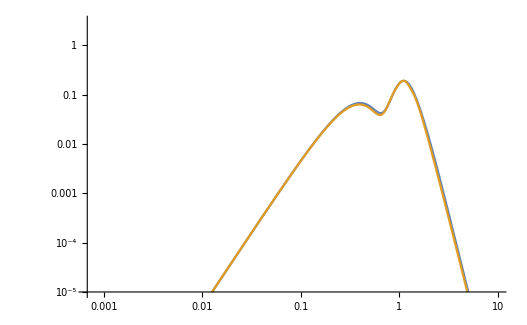

```mathematica
ListLogLogPlot[{ΩPiN,ListPi},PlotRange->{10^-5,3},Joined->True]
```

## The second part of Ω(ρ,x)

Then we evaluate the second line of Eq.(C2). 
x=√((3z)/2);z=2/3 x^2;q→(√(3z))/2 k;*)
((1-3 z)^2(-2+z)^2)/z^(17/2)(-2 z+(-2+z)Log[-1+z])^2

### Define I(a,l,z)

```mathematica
I2[a_,z_,0]:=Piecewise[{{Log[z],a==-1}},z^(1+a)/(1+a)]
I2Inf[a_,0]:=0
```

```mathematica
I2[a_,z_,2]:=Piecewise[{{0,z==1},{Log[-1+z]^2 Log[z]+2 Log[-1+z] PolyLog[2,1-z]-2 PolyLog[3,1-z],a==-1}}
,2(-1+z) HypergeometricPFQ[{1,1,1,-a},{2,2,2},1-z]-2 (-1+z) HypergeometricPFQ[{1,1,-a},{2,2},1-z] Log[-1+z]+((-1+z^(1+a)) Log[-1+z]^2)/(1+a)]
I2[a_,z_,1]:=Piecewise[{{0,a==-1&&z==1},{-(EulerGamma+PolyGamma[0,-1-a])/(1+a),Element[a,NegativeIntegers]&&z==1},{-(EulerGamma+ⅈ π+PolyGamma[0,2+a])/(1+a),z==1},
{Log[-1+z] Log[z]+PolyLog[2,1-z],a==-1},{(z^(1+a) (LerchPhi[1/z,1,-1-a]+Log[-1+z]))/(1+a),Element[a,NegativeIntegers]}},(Beta[z,2+a,0]+z^(1+a) Log[-1+z])/(1+a)]
```

```mathematica
(*a<-5/2*)(*I(a,l,z->∞)*)
I2Inf[a_,2]:=-(π^2+6 HarmonicNumber[-2-a]^2+6 PolyGamma[1,-1-a])/(6+6 a)
I2Inf[a_,1]:=Piecewise[{{0,Element[a,NegativeIntegers]}},(π (-I+Cot[a π]))/(1+a)]
```

### result of the second part

```mathematica
IntLogRho[ρ_,x_]:=1/9 √(2/3)(3/2)^(ρ/2) Sum[Binomial[2,m]Binomial[2+l,n]Binomial[2,l](-3)^m(-2)^(4-n)Re[I2[-13/2+m+n-l+ρ/2,2/3 x^2,l]],{m,0,2},{l,0,2},{n,0,2+l}]
(*z->∞*)
IntLogRhoInf[ρ_]:=1/9 √(2/3)(3/2)^(ρ/2)Sum[Binomial[2,m]Binomial[2+l,n]Binomial[2,l](-3)^m(-2)^(4-n)Re[I2Inf[-13/2+m+n-l+ρ/2,l]],{m,0,2},{l,0,2},{n,0,2+l}]
```

### Contribution to Ω_gw

```mathematica
R1=Max[(√2 km)/k,(√6)/2];R3=Max[(√2 kp)/k,(√6)/2];R2=Max[(√2)/k,(√6)/2];
```

```mathematica
(*κ_-<q<κ_+*)
```

```mathematica
IntLogPeak0=(8 √4)/((225 4+64 k^2(α β-4))^(3/2))(225 √2 4(IntLogRho[0,R3]-IntLogRho[0,R1])+64 k^3(α β-4)(IntLogRho[1,R3]-IntLogRho[1,R1]));
IntLogMinus=(Pkm^2-1)/((km^β-1)^2)(8 √4)/((225 4+64 k^2(α β-4))^(3/2))(225 √2 4Sum[Binomial[2,j](-1)^j(k/(√2))^(j β)(IntLogRho[j β,R2]-IntLogRho[j β,R1]),{j,0,2}]+64 k^3(α β-4)Sum[Binomial[2,j](-1)^j(k/(√2))^(j β)(IntLogRho[j β+1,R2]-IntLogRho[j β+1,R1]),{j,0,2}]);
IntLogPlus=(Pkp^2-1)/((kp^-α-1)^2)(8 √4)/((225 4+64 k^2(α β-4))^(3/2))(225 √2 4Sum[Binomial[2,j](-1)^j(k/(√2))^(-j α)(IntLogRho[-j α,R3]-IntLogRho[-j α,R2]),{j,0,2}]+64 k^3(α β-4)Sum[Binomial[2,j](-1)^j(k/(√2))^(-j α)(IntLogRho[-j α+1,R3]-IntLogRho[-j α+1,R2]),{j,0,2}]);
```

```mathematica
(*q<κ_-*)
```

```mathematica
IntLogIR=(k/(√2))^(2 α)(1+λ)^2 am Sum[Binomial[2,j]((2^(1/2 (-α-β)) k^(α+β) km^(-2 α-β) (-1+Pkm))/(1+λ))^j(IntLogRho[2α+j(α+β),R1]-IntLogRho[2α+j(α+β),(√6)/2]),{j,0,2}]+
(k/(√2))^(2 α)(1+λ)^2 bm Sum[Binomial[2,j]((2^(1/2 (-α-β)) k^(α+β) km^(-2 α-β) (-1+Pkm))/(1+λ))^j(IntLogRho[2α+j(α+β)-2,R1]-IntLogRho[2α+j(α+β)-2,(√6)/2]),{j,0,2}];
```

```mathematica
(*q>κ_+*)
```

```mathematica
IntLogUV=((k/(√2))^(-2 β)(1+λ^-1)^2 )  (8 √2)/15 Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(IntLogRhoInf[-2β-j(α+β)]-IntLogRho[-2β-j(α+β),R3]),{j,0,2}]+
((k/(√2))^(-2 β)(1+λ^-1)^2 )  ap Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(IntLogRhoInf[-2β-j(α+β)-2]-IntLogRho[-2β-j(α+β)-2,R3]),{j,0,2}]+((k/(√2))^(-2β)(1+λ^-1)^2 )  bp Sum[Binomial[2,j]((2^((α+β)/2) k^(-α-β) kp^(α+2 β) (-1+Pkp))/(1+λ^-1))^j(IntLogRhoInf[-2β-j(α+β)-4]-IntLogRho[-2β-j(α+β)-4,R3]),{j,0,2}];
```

### Numerical & Graphic

```mathematica
(*ListLog=ParallelTable[{j,Block[{$MaxExtraPrecision=500},Re[N[IntLogUV/.k->j,10]]+Re[N[IntLogIR/.k->j,10]]+Re[N[IntLogPlus/.k->j,10]]+Re[N[IntLogMinus/.k->j,10]]+Re[N[IntLogPeak0/.k->j,10]]]},{j,kRange}];*)
ListLog=ParallelTable[{j,Block[{$MaxExtraPrecision=500},
N[Re[IntLogUV]+Re[IntLogIR]+Re[IntLogPlus]+Re[IntLogMinus]+Re[IntLogPeak0]/.k->j,5
]]},{j,kRange}];
```

```mathematica
(*Numerical result*)
```

```mathematica
IntFuncLog=(3 (1-2 x^2)^2 (1-2 y^2)^2 (-3+x^2+y^2)^4 ((2 (x-y) (x+y))/(-3+x^2+y^2)+Log[(3-2 y^2)/(2 x^2-3)])^2)/(4 (x-y)^8 (x+y)^8)(2^β  k^(2 α) (x^2-y^2)^α (α+β)^2)/(((k(x-y))^(α+β) α+2^((α+β)/2) β) ((k(x+y))^(α+β) α+2^((α+β)/2) β))//Simplify;
```

```mathematica
ΩLogN=ParallelTable[{j,NIntegrate[IntFuncLog/.k->j,{x,(√6)/2,√3,+∞},{y,(-√2)/2,(√2)/2},WorkingPrecision->50,AccuracyGoal->15,PrecisionGoal->8]},{j,kRange}];
```

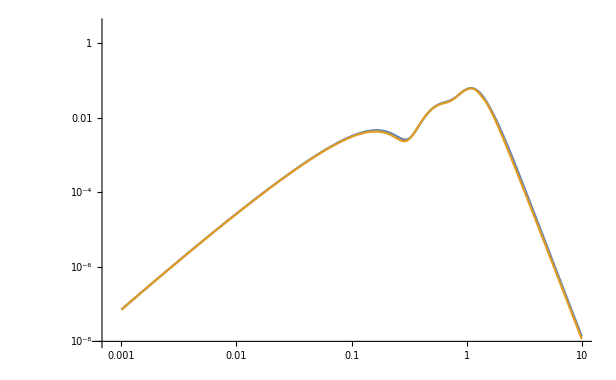

```mathematica
ListLogLogPlot[{ΩLogN,ListLog},PlotRange->{10^-8,3},Joined->True]
```

## Ω_GW^(√2/2+)

### Integration

```mathematica
I1UV[p_,q_,r_,x_]:=Piecewise[{{-x^(1-q+r)/(p q+p^2 q x^q)+((-1+q-r) x^(1-2 q+r) LerchPhi[-x^-q/p,1,2-(1+r)/q])/(p^2 q^2),Element[(1+r)/q,NonPositiveIntegers]}},(x^(1+r) Hypergeometric2F1[2,(1+r)/q,1+(1+r)/q,-p x^q])/(1+r)]
```

### Result

```mathematica
p=α/β 2^(-(α+β)/2)k^(α+β);  
Cp=2^-α k^(2 α)(α+β)^2/β^2;
ConstUV1=Cp 2400 (2-5 Log[3]+Log[32])^2;
```

```mathematica
(*αβ>3*)

IntUV1=ConstUV1 (√π Erf[1])/(√α √β)Sum[Binomial[2,m](-1)^m 2^(-(2-m)/2)(I1UV[p,α+β,m+2α+1,(√6)/2]-I1UV[p,α+β,m+2α+1,(√2)/2]),{m,0,2}];
```

```mathematica
ListUV1=ParallelTable[{j,N[IntUV1/.k->j,20]},{j,kRange}];
```

## Ω_GW^(ν->0)

```mathematica
ConstUV2=(16 k^(2 α) (α+β)^2)/(45 β (k^(α+β) α+β));
IntUV2=2 ConstUV2(v^(4+α) Hypergeometric2F1[1,(4+α)/(α+β),1+(4+α)/(α+β),-α/β k^(α+β) v^(α+β)])/(4+α)/.v->(√3-1)/2;
```

```mathematica
ListUV2=ParallelTable[{j,Re[N[IntUV2/.k->j,10]]},{j,kRange}];
```

## Ω_GW^(√6/2-)

```mathematica
ConstUV3=(8 √6)/(27 E^2)((α+β)/(α ((√3)/2 k)^β+β ((√3)/2 k)^-α))^2;
IntUV3=ConstUV3 Q1m;
```

```mathematica
ListUV3=ParallelTable[{j,N[IntUV3/.k->j,20]},{j,kRange}];
```

## result of Ω_GW^(√6/2-)+Ω_GW^(ν->0)+Ω_GW^(√2/2+) (compared with numeric result)

```mathematica
(*Analytical result*)
```

```mathematica
ListUV=ParallelTable[ {kRange[[j]],Re[ListUV1[[j,2]]+ListUV2[[j,2]]+ListUV3[[j,2]]]},{j,Length@kRange}];
```

```mathematica
(*Numerical result*)
```

```mathematica
IntFuncUV=(3 (1-2 x^2)^2 (1-2 y^2)^2 (-3+x^2+y^2)^4 ((2 (x-y) (x+y))/(-3+x^2+y^2)+Log[(3-2 y^2)/(3-2 x^2)])^2)/(4 (x-y)^8 (x+y)^8)(2^β  k^(2 α) (x^2-y^2)^α (α+β)^2)/(((k(x-y))^(α+β) α+2^((α+β)/2) β) ((k(x+y))^(α+β) α+2^((α+β)/2) β))//Simplify;
```

```mathematica
ΩUV=ParallelTable[{j,NIntegrate[IntFuncUV/.k->j,{x,(√2)/2,(√6)/2},{y,(-√2)/2,(√2)/2},WorkingPrecision->10]},{j,kRange}];
```

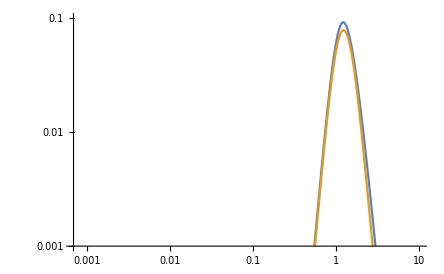

```mathematica
ListLogLogPlot[{ΩUV,ListUV},PlotRange->{10^-3,10^-1},Joined->True]
```

## Final Result

```mathematica
(*Ogw*)
```

```mathematica
(*Analytical*)
ListAll=Table[{kRange[[j]],ListUV[[j,2]]+ListPi[[j,2]]+ListLog[[j,2]]},{j,Length@kRange}];
(*Numerical*)
ΩAll=Table[{kRange[[j]],ΩUV[[j,2]]+ΩPiN[[j,2]]+ΩLogN[[j,2]]},{j,Length@kRange}];
```

### LogNormal

```mathematica
PLN=Exp[-1/(2 ΔLN^2)(Log[k/(√2)(x+y)]^2+Log[k/(√2)(x-y)]^2)];
IntFuncLN1=1/(4 (x-y)^8 (x+y)^8)3 (1-2 x^2)^2 (1-2 y^2)^2 (-3+x^2+y^2)^4 (π^2 HeavisideTheta[-3+√6 x]+((2 (x-y) (x+y))/(-3+x^2+y^2)+Log[(3-2 y^2)/Abs[3-2 x^2]])^2)PLN;
```

```mathematica
ΩLN=ParallelTable[{j,NIntegrate[IntFuncLN1/.k->j,{x,(√2)/2,(√6)/2,√3,+∞},{y,(-√2)/2,(√2)/2},PrecisionGoal->3]},{j,kRangeLN}];
(*This is the SIGW generated by a log-normal spectrum, this step takes about 5 minutes*)
```

### Graphic

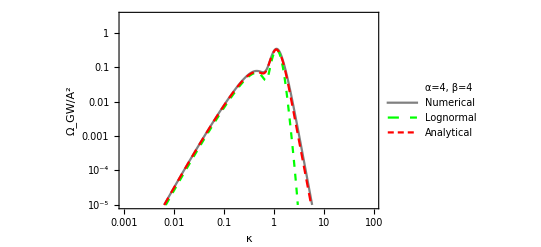

```mathematica
ListLogLogPlot[{{{0,0}},ΩAll,ΩLN,ListAll},PlotRange->{{10^-3,10^2},{10^-5,3}},Joined->True,PlotStyle->{White,Gray,{Green,Dashed},{Red,Dashing[{0.015,0.01}]}(*,{Green,Dashed}*)},Frame->True,PlotLegends->Placed[{"α=4, β=4","Numerical","Lognormal","Analytical"},Scaled[{0.5,0.23}]],FrameLabel->{κ,"Ω_GW/A^2"}(*,PlotLabel->"α=4, β=1/2"*)(*,
GridLines->{{2},{0.14,0.14 10^-1,0.14 10^-2,0.14 10^-3}}*)(*,GridLines->{{2},{0.24,0.24 10^-1,0.24 10^-2}}*)]
```